```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/Книга3.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/~$Книга3.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/351/Книга3.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"I"->(Around[#I, #dI] &),"V"-> (Around[#V, #dV] &)|>]
```

Dataset[<>]

```mathematica
line1 =LinearModelFit[(Normal@dataset1[All,{"I","V"}/*Values])⟦5;;9⟧,{1,x},x]
```

FittedModel[45.8248-10.6307 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 45.8248 | 0.797034 | 57.4942 | 0.0000115911
x | -10.6307 | 0.469006 | -22.6665 | 0.000188053

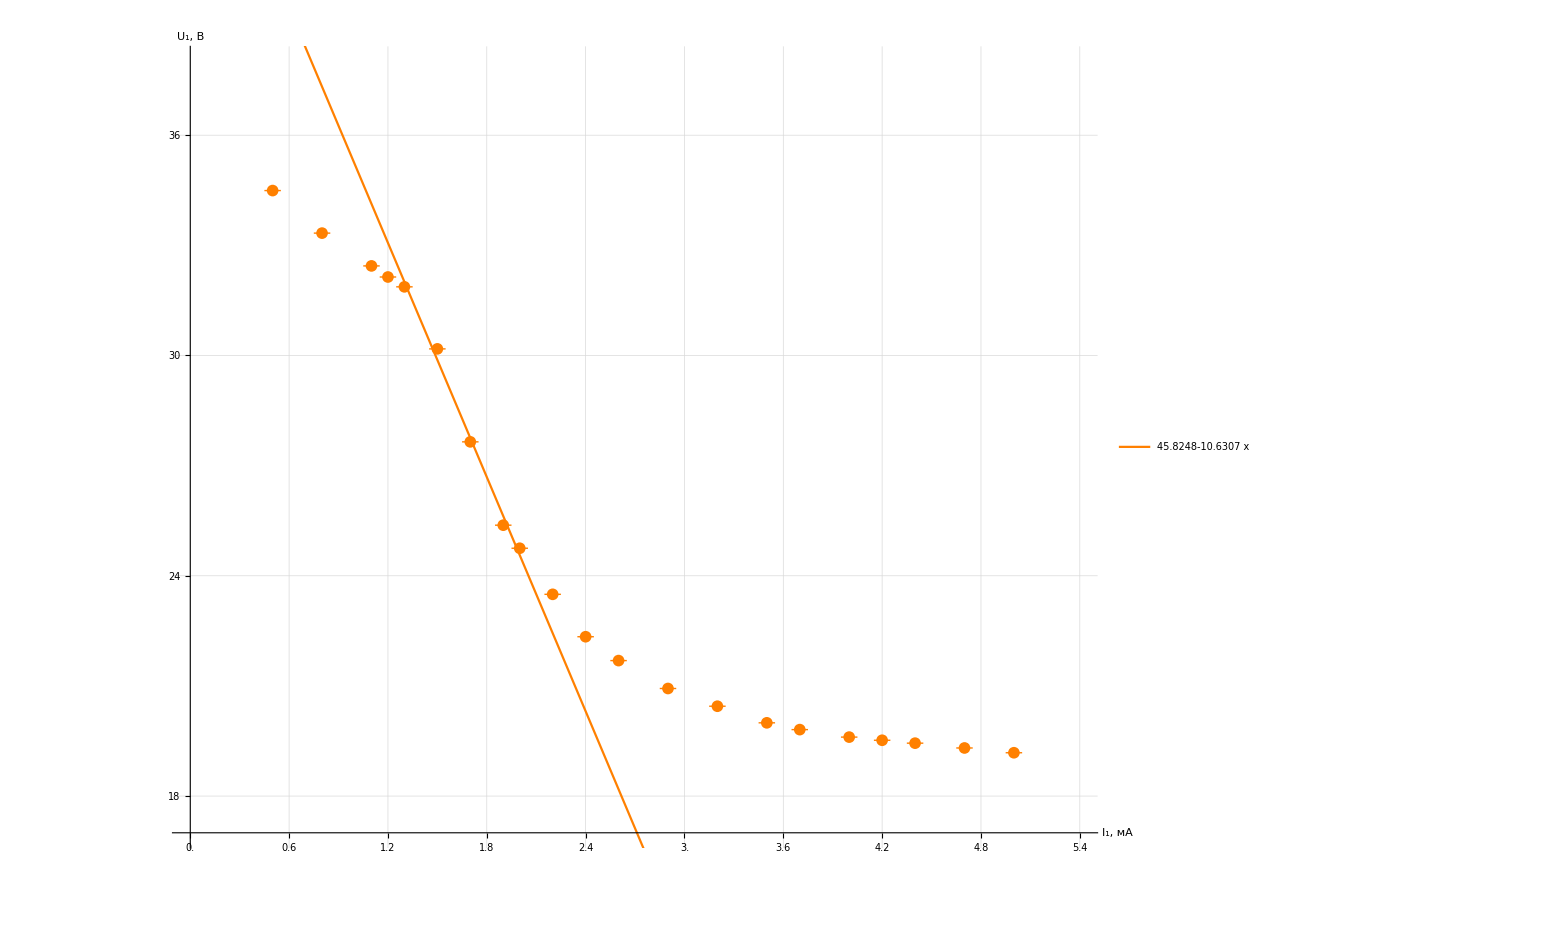

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
Ticks-> {Range[0,50,0.2],Range[0,1300,2]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["I_1, мА",Large],Style["U_1, B",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0,5.4},{17,38}},

GridLines->{Range[-0.1,10,0.1], Range[-10,50,0.5]},
LabelStyle->Black,
PlotStyle->Orange
],
Plot[
{line1@x},
{x,0, 50},
PlotLegends->Placed[
LineLegend[
{Normal@line1, line1["ParameterTable"]},
LabelStyle->20
],
{Scaled[0.5],Scaled[0.75]}
],
PlotStyle->Orange
]
]
```

## Dataset2

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs,line1,dataset3]
```

```mathematica
dataset1=makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
|
```

```mathematica
line1 =LinearModelFit[(Normal@dataset1[All,{"U","I"}/*Values])⟦1;;5⟧,{1,x},x]
```

FittedModel[79.6559+1.21375 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 79.6559 | 1.71277 | 46.507 | 0.0000218874
x | 1.21375 | 0.087792 | 13.8253 | 0.000819086

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦6⟧]
```

Dataset[<>]

```mathematica
line2 =LinearModelFit[(Normal@dataset2[All,{"U","I"}/*Values])⟦1;;6⟧,{1,x},x]
```

FittedModel[40.49+0.833599 x]

```mathematica
line2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 40.49 | 0.97803 | 41.3995 | 2.03461×10^-6
x | 0.833599 | 0.0535268 | 15.5735 | 0.0000992575

## Dataset3

```mathematica
dataset3=makeDataset[raw⟦7⟧]
```

Dataset[<>]

```mathematica
line3 =LinearModelFit[(Normal@dataset3[All,{"U","I"}/*Values])⟦1;;6⟧,{1,x},x]
```

FittedModel[19.642+0.469708 x]

```mathematica
line3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 19.642 | 0.344409 | 57.031 | 5.66×10^-7
x | 0.469708 | 0.0188208 | 24.9569 | 0.0000153023

```mathematica
Show[
ListPlot[
{dataset1,dataset2,dataset3},
Ticks-> {Range[-100,100,2],Range[-1000,1300,10]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["U_2, В",Large],Style["I_2, мкА",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{-30,30},{-125,125}},

GridLines->{Range[-200,200,1], Range[-200,200,4]},
LabelStyle->Black
, Joined->True,
InterpolationOrder->1 ,
PlotLegends->Placed[LineLegend[
Automatic,
{"I_p = 5 мА","I_p = 3 мА","I_p = 1,5 мА"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.1],Scaled[0.75]}
]
],
Plot[
{line1@x,line2@x,line3@x},
{x,0, 25},
PlotLegends->Placed[
LineLegend[
{Normal@line1, Normal@line2,Normal@line3},
LegendLabel->"I_(i:043d)",
LabelStyle->20,
LegendFunction->frame
],
{Scaled[0.3],Scaled[0.75]}
]
],
Plot[
{line4@x,line5@x,line6@x},
{x,-40, 40},
PlotLegends->Placed[
LineLegend[
{Normal@line4, Normal@line5,Normal@line6},
LabelStyle->20,
LegendFunction->frame,
LegendLabel->"(dI/dU)_(u = 0)"
],
{Scaled[0.7],Scaled[0.3]}
]
],
ListPlot[{{Callout[{x1,line4@x1},x1,{4,100},LabelStyle->14,Background->None]},
{Callout[{x2,line5@x2},x2,{8,55},,LabelStyle->14,Background->None]},
{Callout[{x3,line6@x3},x3,{10,10},,LabelStyle->14,Background->None]}},
PlotStyle->Automatic,
PlotMarkers->{Automatic,14}
]
]
```

-Graphics-

```mathematica
line4 =LinearModelFit[(Normal@dataset1[All,{"U","I"}/*Values])⟦10;;13⟧,{1,x},x]
```

FittedModel[3.15168+16.9958 x]

```mathematica
line4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.15168 | 4.12453 | 0.76413 | 0.524632
x | 16.9958 | 2.76256 | 6.15217 | 0.0254176

```mathematica
line5 =LinearModelFit[(Normal@dataset2[All,{"U","I"}/*Values])⟦10;;14⟧,{1,x},x]
```

FittedModel[1.85596+7.32579 x]

```mathematica
line5["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.85596 | 0.71381 | 2.60008 | 0.0803702
x | 7.32579 | 0.320788 | 22.8369 | 0.000183896

```mathematica
line6 =LinearModelFit[(Normal@dataset3[All,{"U","I"}/*Values])⟦9;;15⟧,{1,x},x]
```

FittedModel[0.695734+3.37929 x]

```mathematica
line6["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.695734 | 0.277298 | 2.50897 | 0.0538955
x | 3.37929 | 0.0831884 | 40.6221 | 1.70482×10^-7

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

```mathematica
x1 = (x/.Solve[Normal@line1==Normal@line4,x])⟦1⟧
```

4.84755

```mathematica
x2=(x/.Solve[Normal@line2==Normal@line5,x])⟦1⟧
```

5.95085

```mathematica
x3 = (x/.Solve[Normal@line3==Normal@line6,x])⟦1⟧
```

6.51169

```mathematica
line1@x1
```

85.5396

```mathematica
Dot
```

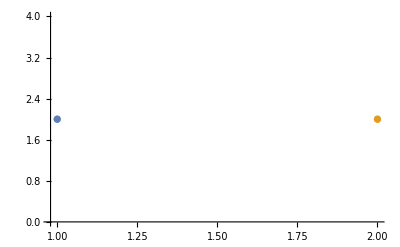

```mathematica
ListPlot[{{{1,2}},{{2,2}}}
]
```

```mathematica
StringJoin["a","b"]
```

ab

```mathematica
"a"+"b"
```

a+b

```mathematica
StringJoin["U_1 = ",ToString@x1]
```

U_1 = 4.84755

## Otherway

```mathematica
data1= {{Around[5,0.1],Around[2.3434,0.381]},{Around[3,0.1],Around[2.7635, 0.1382]},{Around[1.5,0.1],Around[2.9,0.0878]}}
```

{{5.000.10,2.30.4},{3.000.10,2.760.14},{1.500.10,2.900.09}}

```mathematica
line1=LinearModelFit[{{5,2.3434},{3,2.7635},{1.5,2.9}},{1,x},x]
```

FittedModel[3.18129-0.161786 x]

```mathematica
data2= {{Around[5,0.1],Around[8.3895,0.9812]},{Around[3,0.1],Around[3.92699, 0.154]},{Around[1.5,0.1],Around[1.8577,0.056]}}
```

{{5.000.10,8.41.0},{3.000.10,3.930.15},{1.500.10,1.860.06}}

```mathematica
line2=LinearModelFit[{{5,8.3895},{3,3.92699},{1.5,1.8577}},{1,x},x]
```

FittedModel[-1.24748+1.88596 x]

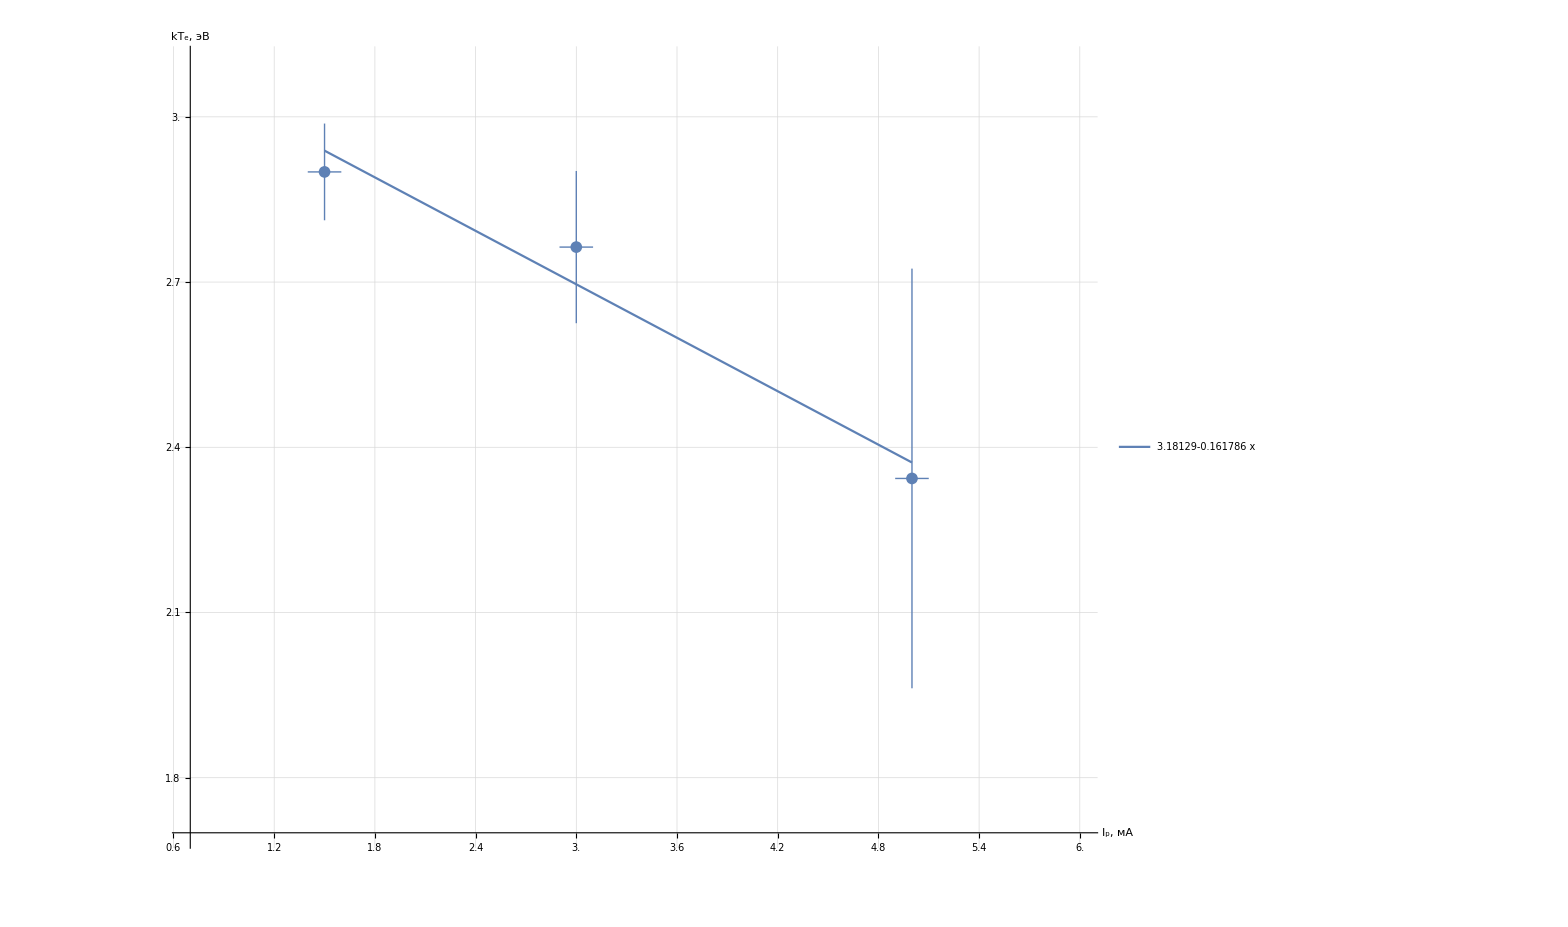

```mathematica
Show[
ListPlot[
{data1},
Ticks-> {Range[0,50,0.2],Range[0,1300,0.1]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["I_p, мА",Large],Style["kT_e, эB",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0.7,6},{1.7,3.1}},

GridLines->{Range[-0.1,10,0.1], Range[-10,50,0.05]},
LabelStyle->Black
],
Plot[
{line1@x},
{x,1.5, 5},
PlotLegends->Placed[
LineLegend[
{Normal@line1, line1["ParameterTable"]},
LabelStyle->20
],
{Scaled[0.4],Scaled[0.4]}
]
]
]
```

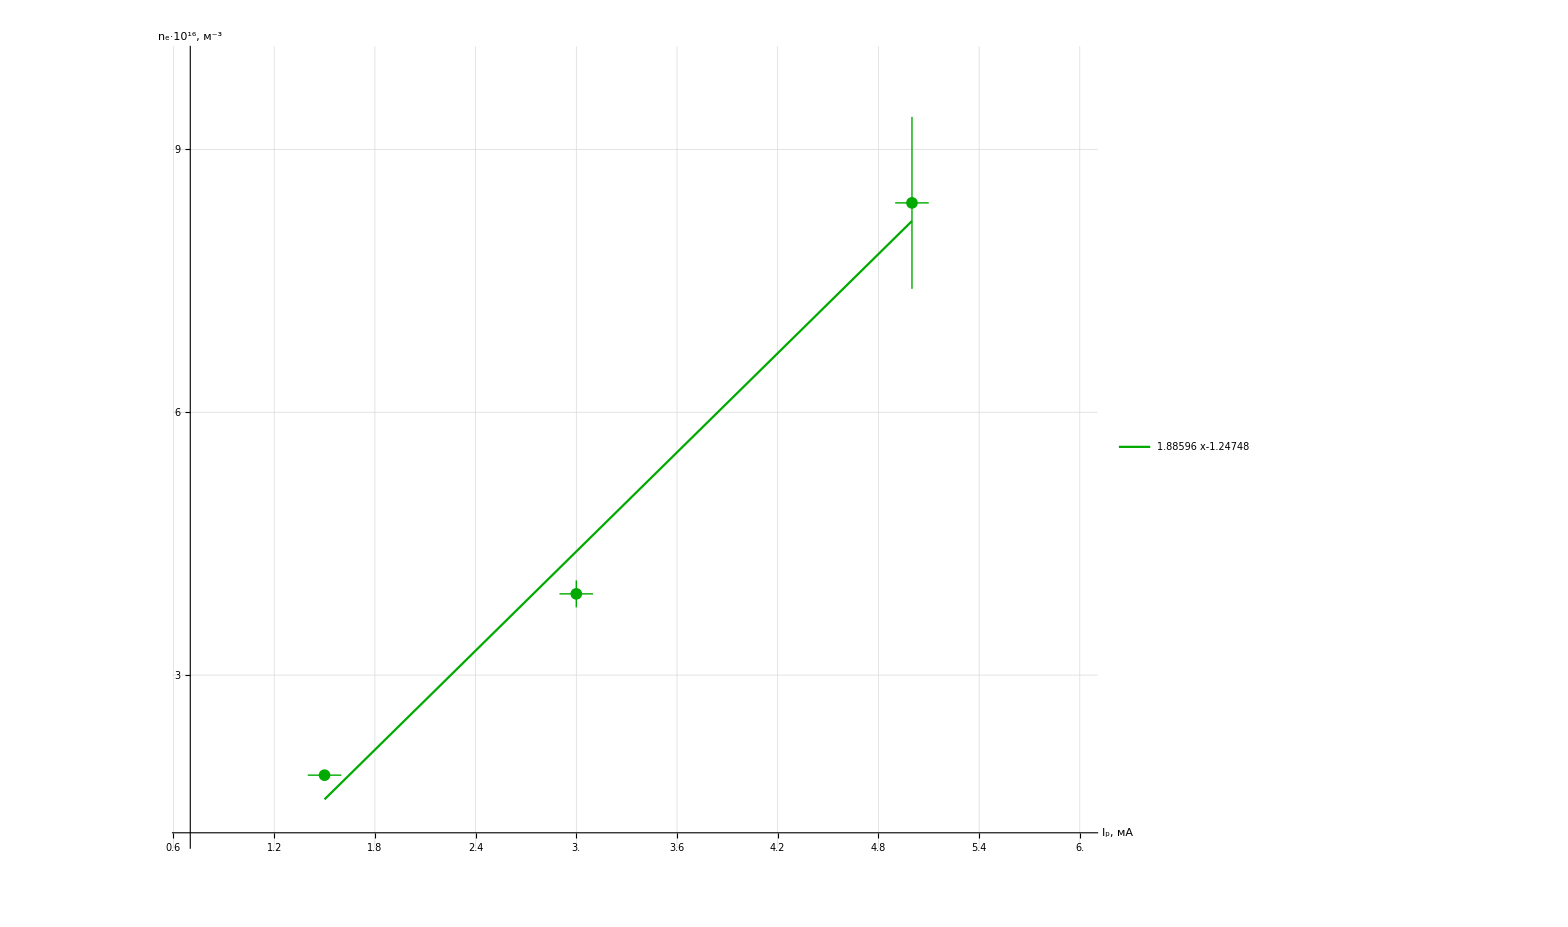

```mathematica
Show[
ListPlot[
{data2},
Ticks-> {Range[0,50,0.2],Range[0,1300,1]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["I_p, мА",Large],Style["n_e·10^16, (:043c)^-3",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0.7,6},{1.2,10}},

GridLines->{Range[-0.1,10,0.1], Range[-10,50,0.2]},
LabelStyle->Black,
PlotStyle->Darker@Green
],
Plot[
{line2@x},
{x,1.5, 5},
PlotLegends->Placed[
LineLegend[
{Normal@line2, line1["ParameterTable"]},
LabelStyle->20
],
{Scaled[0.4],Scaled[0.6]}
],
PlotStyle->Darker@Green
]
]
```

```mathematica
\Rawdot
```

```mathematica
\[FilledSmallCircle]paclet:ref/character/FilledSmallCirclepaclet:ref/character/RawDot
```

```mathematica
·
```